```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
```

```mathematica
(* INITIALIZING PARAMETERS *)
uq=0.315 (* up quark mass *);
sq=0.577 (* strange quark mass *);
cq=1.836(* charm quark mass *);
bq=5.227 (* bottom quark mass *);
sigma=0.1653; (* coefficient of string strength term *)
alphaCoulomb=0.5069; (* coefficient of Coulomb term (0.0175) if you want to replicate Roberts *)
Cqqq=-0.8321(* V = -Subscript[α, C]/r + σr + Subscript[C, qqq] *);
κp=1.8609(* Thing in the spin term *);
CF=1/2(* Colour Factor *);
```

```mathematica
(* INITIALIZING HYPERPARAMETERS *)
γMax=6;
Λ=0;
m1=uq;
m2=sq;
m3=cq;
t1=tMatrix[Λ,γMax,1];
t2=tMatrix[Λ,γMax,2];
size=Dimensions[t1][[1]];
ω=0.44;
r0[mi_,mj_]:=1.6553((2mi mj)/(mi+mj))^-0.2204(* Gaussian function parameter *);
```

```mathematica
(* Perturbative spin term *)
radialPart12=(8 Pi)/(3m1 m2 r0[m1,m2]^3 Pi^(3/2))κp GaussOperator[Λ,γMax,ω,3,m1,m2];
radialPart23=(8 Pi)/(3m2 m3 r0[m2,m3]^3 Pi^(3/2))κp Transpose[t1].GaussOperator[Λ,γMax,ω,1,m2,m3].t1;
radialPart31=(8 Pi)/(3m3 m1 r0[m3,m1]^3 Pi^(3/2))κp Transpose[t2].GaussOperator[Λ,γMax,ω,2,m3,m1].t2;
radialPartList={radialPart12,radialPart23,radialPart31};
spinPartList={1/4,1/4,1/4};
spinTermTotal=Total[radialPartList*spinPartList];
```

```mathematica
(* THIS FUNCTION RETURNS THE BARYON HAMILTONIAN FOR A GIVEN ω *)
baryonHamiltonian[omega_]:=(
ω=omega;
vCoulomb=polynomialOperatorRho[Λ,γMax,-1];
vLinear=polynomialOperatorRho[Λ,γMax,1];
v12baryon=-alphaCoulomb*α*vCoulomb+(sigma*vLinear)/α;
v23baryon=-alphaCoulomb*α1*(Transpose[t1].vCoulomb.t1)+(sigma*(Transpose[t1].vLinear.t1))/α1;
v31baryon=-alphaCoulomb*α2*(Transpose[t2].vCoulomb.t2)+(sigma*(Transpose[t2].vLinear.t2))/α2;
kin=kMatrix[Λ,γMax,omega];
mas1=IdentityMatrix[size]*m1;
mas2=IdentityMatrix[size]*m2;
mas3=IdentityMatrix[size]*m3;
cqqq=IdentityMatrix[size]*(Cqqq);
Hbaryon=mas1+mas2+mas3+kin+CF(v12baryon+v23baryon+v31baryon+3*cqqq))
```

```mathematica
Rcoeff[0,0]*Rcoeff[0,0]*Lcoeff[0,0,0]*Lcoeff[0,0,0]*Gamma[3/2]/(2(1+1/(r0[m1,m2]^2 α^2))^(3/2))
```

0.128269

```mathematica
GaussOperator[0,4,ω,3,m1,m2]//MatrixForm
```

(0.128269 | 0. | 0. | 0.117141 | 0. | 0. | 0. | 0. | 0. | 0.097657
0. | 0.128269 | 0. | 0. | 0. | 0. | 0. | 0.117141 | 0. | 0.
0. | 0. | 0.0326237 | 0. | 0. | 0. | 0. | 0. | 0.0384632 | 0.
0.117141 | 0. | 0. | 0.115275 | 0. | 0. | 0. | 0. | 0. | 0.10302
0. | 0. | 0. | 0. | 0.128269 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0326237 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0082975 | 0. | 0. | 0.
0. | 0.117141 | 0. | 0. | 0. | 0. | 0. | 0.115275 | 0. | 0.
0. | 0. | 0.0384632 | 0. | 0. | 0. | 0. | 0. | 0.0474582 | 0.
0.097657 | 0. | 0. | 0.10302 | 0. | 0. | 0. | 0. | 0. | 0.0979552)

```mathematica
sigma*rel[0,0,0,-1]/α
```

0.681932

```mathematica
sigma*α^-1*polynomialOperatorRho[0,4,1]//MatrixForm
```

(0.681932 | 0. | 0. | -0.278397 | 0. | 0. | 0. | 0. | 0. | -0.0622516
0. | 0.681932 | 0. | 0. | 0. | 0. | 0. | -0.278397 | 0. | 0.
0. | 0. | 0.909242 | 0. | 0. | 0. | 0. | 0. | -0.287528 | 0.
-0.278397 | 0. | 0. | 1.0229 | 0. | 0. | 0. | 0. | 0. | -0.381211
0. | 0. | 0. | 0. | 0.681932 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.909242 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1.09109 | 0. | 0. | 0.
0. | -0.278397 | 0. | 0. | 0. | 0. | 0. | 1.0229 | 0. | 0.
0. | 0. | -0.287528 | 0. | 0. | 0. | 0. | 0. | 1.18201 | 0.
-0.0622516 | 0. | 0. | -0.381211 | 0. | 0. | 0. | 0. | 0. | 1.27862)

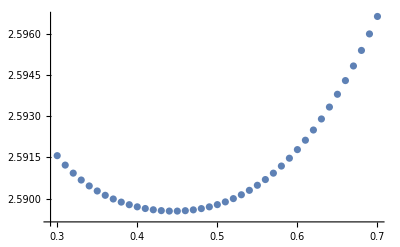

```mathematica
ListPlot[Table[{ω,Eigenvalues[baryonHamiltonian[ω]][[-1]]-(2.02*10^-3)/(m1*m2*m3)},{ω,0.3,0.7,0.01}]]
```

```mathematica
h=baryonHamiltonian[ω];
eigenVec=Eigenvectors[h];
eigenVal=Eigenvalues[h];
correction=eigenVec[[-1]].spinTermTotal.eigenVec[[-1]]
```

```mathematica
eigenVec[[-1]]
```

{0.977041,-0.181625,0.0390616,-0.00474356,0.0754663,-0.020581,0.0298361,0.0368011,0.00659325,0.0450639,-0.0139533,-0.0000436488,0.00447369,0.0030629,0.000770318,0.00328096,0.00533472,-0.00329778,0.00389166,0.0112671}

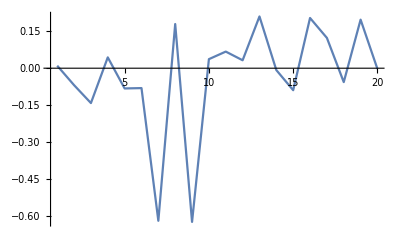

```mathematica
ListPlot[eigenVec[[-8]],Joined->True,PlotRange->All]
```

```mathematica
eigenVal[[-1]]+CF*correction-(2.02*10^-3)/(m1*m2*m3)
```

2.64916

```mathematica
eigenVal[[-1]]-(2.02*10^-3)/(m1*m2*m3)
```

2.58954

```mathematica
m1+m2+m3
```

2.728

```mathematica
(* THIS FUNCTION RETURNS THE BARYON HAMILTONIAN FOR A GIVEN ω and γ *)
baryonHamiltonian2[omega_,γ_]:=(
ω=omega;
γMax=γ;
t1=tMatrix[Λ,γMax,1];
t2=tMatrix[Λ,γMax,2];
size=Dimensions[t1][[1]];
vCoulomb=polynomialOperatorRho[Λ,γMax,-1];
vLinear=polynomialOperatorRho[Λ,γMax,1];
v12baryon=-alphaCoulomb*α*vCoulomb+(sigma*vLinear)/α;
v23baryon=-alphaCoulomb*α1*(Transpose[t1].vCoulomb.t1)+(sigma*(Transpose[t1].vLinear.t1))/α1;
v31baryon=-alphaCoulomb*α2*(Transpose[t2].vCoulomb.t2)+(sigma*(Transpose[t2].vLinear.t2))/α2;
kin=kMatrix[Λ,γMax,omega];
mas1=IdentityMatrix[size]*m1;
mas2=IdentityMatrix[size]*m2;
mas3=IdentityMatrix[size]*m3;
cqqq=IdentityMatrix[size]*(Cqqq);
Hbaryon=mas1+mas2+mas3+kin+v12baryon+v23baryon+v31baryon+cqqq)
```

```mathematica
(* Optimises the lowest lying eigenvalue (searches for best ω) *)
baryonMinimumEigenvalue[gammaMax_,Lambda_,mass1_,mass2_,mass3_]:=(
γMax=gammaMax;
Λ=Lambda;
m1=mass1;
m2=mass2;
m3=mass3;
t1=tMatrix[Λ,gammaMax,1]; (* transformation matrix 1 *)
t2=tMatrix[Λ,gammaMax,2];(* transformation matrix 2 *)
size=Dimensions[t1][[1]]; (* size of matrix *)
table=Table[{Eigenvalues[baryonHamiltonian[ω]][[-1]],ω},{ω,0.01,0.5,0.01}];
PlotPoints[table]
)
```

```mathematica
baryonMinimumEigenvalue[4,0,m1,m2,m3]
```

PlotPoints[{{5.35877,0.01},{4.15025,0.02},{3.62649,0.03},{3.32359,0.04},{3.12449,0.05},{2.98387,0.06},{2.87995,0.07},{2.80078,0.08},{2.73916,0.09},{2.69046,0.1},{2.65155,0.11},{2.6202,0.12},{2.59479,0.13},{2.57411,0.14},{2.55723,0.15},{2.54341,0.16},{2.53209,0.17},{2.5228,0.18},{2.51517,0.19},{2.50889,0.2},{2.50372,0.21},{2.49946,0.22},{2.49594,0.23},{2.49302,0.24},{2.4906,0.25},{2.48858,0.26},{2.48689,0.27},{2.48547,0.28},{2.48427,0.29},{2.48325,0.3},{2.48239,0.31},{2.48164,0.32},{2.481,0.33},{2.48044,0.34},{2.47996,0.35},{2.47955,0.36},{2.47918,0.37},{2.47887,0.38},{2.4786,0.39},{2.47837,0.4},{2.47819,0.41},{2.47804,0.42},{2.47793,0.43},{2.47785,0.44},{2.47782,0.45},{2.47782,0.46},{2.47786,0.47},{2.47794,0.48},{2.47806,0.49},{2.47823,0.5}}]

```mathematica
(√3)/4(-3/4)-(√3)/4(1/4)//Simplify
```

-(√3)/4

```mathematica
Pi*(0.25)^2
```

0.19635

```mathematica
Pi(7.5)^2*30
```

5301.44

```mathematica
5301/0.196
```

27045.9

```mathematica
3/4(-3/4)+1/4(1/4)
```

-1/2

```mathematica
1/4(-3/4)+3/4(1/4)
```

0

```mathematica
3/4(-3/4)+1/4(1/4)
```

-1/2

```mathematica
1/4(-3/4)+3/4(1/4)
```

0

```mathematica
stateMatrix[1,3]//MatrixForm
```

((0 | 0 | 0 | 1
0 | 0 | 0 | 1) | (0 | 0 | 0 | 1
0 | 1 | 0 | 0) | (0 | 0 | 0 | 1
0 | 0 | 1 | 1) | (0 | 0 | 0 | 1
0 | 1 | 0 | 2) | (0 | 0 | 0 | 1
0 | 1 | 1 | 0) | (0 | 0 | 0 | 1
0 | 2 | 0 | 1) | (0 | 0 | 0 | 1
1 | 0 | 0 | 1) | (0 | 0 | 0 | 1
1 | 1 | 0 | 0)
(0 | 1 | 0 | 0
0 | 0 | 0 | 1) | (0 | 1 | 0 | 0
0 | 1 | 0 | 0) | (0 | 1 | 0 | 0
0 | 0 | 1 | 1) | (0 | 1 | 0 | 0
0 | 1 | 0 | 2) | (0 | 1 | 0 | 0
0 | 1 | 1 | 0) | (0 | 1 | 0 | 0
0 | 2 | 0 | 1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 1) | (0 | 1 | 0 | 0
1 | 1 | 0 | 0)
(0 | 0 | 1 | 1
0 | 0 | 0 | 1) | (0 | 0 | 1 | 1
0 | 1 | 0 | 0) | (0 | 0 | 1 | 1
0 | 0 | 1 | 1) | (0 | 0 | 1 | 1
0 | 1 | 0 | 2) | (0 | 0 | 1 | 1
0 | 1 | 1 | 0) | (0 | 0 | 1 | 1
0 | 2 | 0 | 1) | (0 | 0 | 1 | 1
1 | 0 | 0 | 1) | (0 | 0 | 1 | 1
1 | 1 | 0 | 0)
(0 | 1 | 0 | 2
0 | 0 | 0 | 1) | (0 | 1 | 0 | 2
0 | 1 | 0 | 0) | (0 | 1 | 0 | 2
0 | 0 | 1 | 1) | (0 | 1 | 0 | 2
0 | 1 | 0 | 2) | (0 | 1 | 0 | 2
0 | 1 | 1 | 0) | (0 | 1 | 0 | 2
0 | 2 | 0 | 1) | (0 | 1 | 0 | 2
1 | 0 | 0 | 1) | (0 | 1 | 0 | 2
1 | 1 | 0 | 0)
(0 | 1 | 1 | 0
0 | 0 | 0 | 1) | (0 | 1 | 1 | 0
0 | 1 | 0 | 0) | (0 | 1 | 1 | 0
0 | 0 | 1 | 1) | (0 | 1 | 1 | 0
0 | 1 | 0 | 2) | (0 | 1 | 1 | 0
0 | 1 | 1 | 0) | (0 | 1 | 1 | 0
0 | 2 | 0 | 1) | (0 | 1 | 1 | 0
1 | 0 | 0 | 1) | (0 | 1 | 1 | 0
1 | 1 | 0 | 0)
(0 | 2 | 0 | 1
0 | 0 | 0 | 1) | (0 | 2 | 0 | 1
0 | 1 | 0 | 0) | (0 | 2 | 0 | 1
0 | 0 | 1 | 1) | (0 | 2 | 0 | 1
0 | 1 | 0 | 2) | (0 | 2 | 0 | 1
0 | 1 | 1 | 0) | (0 | 2 | 0 | 1
0 | 2 | 0 | 1) | (0 | 2 | 0 | 1
1 | 0 | 0 | 1) | (0 | 2 | 0 | 1
1 | 1 | 0 | 0)
(1 | 0 | 0 | 1
0 | 0 | 0 | 1) | (1 | 0 | 0 | 1
0 | 1 | 0 | 0) | (1 | 0 | 0 | 1
0 | 0 | 1 | 1) | (1 | 0 | 0 | 1
0 | 1 | 0 | 2) | (1 | 0 | 0 | 1
0 | 1 | 1 | 0) | (1 | 0 | 0 | 1
0 | 2 | 0 | 1) | (1 | 0 | 0 | 1
1 | 0 | 0 | 1) | (1 | 0 | 0 | 1
1 | 1 | 0 | 0)
(1 | 1 | 0 | 0
0 | 0 | 0 | 1) | (1 | 1 | 0 | 0
0 | 1 | 0 | 0) | (1 | 1 | 0 | 0
0 | 0 | 1 | 1) | (1 | 1 | 0 | 0
0 | 1 | 0 | 2) | (1 | 1 | 0 | 0
0 | 1 | 1 | 0) | (1 | 1 | 0 | 0
0 | 2 | 0 | 1) | (1 | 1 | 0 | 0
1 | 0 | 0 | 1) | (1 | 1 | 0 | 0
1 | 1 | 0 | 0))